## Module for varying mass of the projectile and mass of the counterweight

```mathematica
v45[mpr_, mcwt_]:=
Module[{Lcw,Ls,Lb,theta0,phi0,thetashot,Mp=mpr,Mcw =mcwt,Mb,Mbase,Msy,g,Lt,V,theta,t,phi,xp,yp,xcw,ycw,Ib,xpd,ypd,xcwd,ycwd,T,L,sol,x,tmax,thetaDer,xder,vxpro,vypro,xpos,ypos,thetat,tshot,vshot,EL},

EL[q_]:=D[L,q[t]]-D[D[L,q'[t]],t]==0;
Mb=0.045;
theta0 = Pi/4;
phi0 = 0;
Lt=.99;
Lcw=.115;
Ls=.35;
Lb = Lt-Ls;
thetashot=-Pi/4;
Mbase = 0.485;
Msy = Mbase+Mb+Mcw+Mp;
g =9.81;

V= -Mp*Lb* Sin[theta[t]]*g + (Ls*Sin[theta[t]]-Lcw*Cos[phi[t]])*g*Mcw - 1/2 *Sin[theta[t]]*Mb*g*(Lb-Ls);

xp =- Lb *Cos[theta[t]]+x[t];
yp = - Lb*Sin[theta[t]];
xcw = Ls *Cos[theta[t]]+x[t]+Lcw *Sin[phi[t]];
ycw = Ls *Sin[theta[t] ]-Lcw *Cos[phi[t]];
Ib =Mb*1/3 ((Lb^3+Ls^3)/(Lb+Ls));
xpd=D[xp,t];
ypd=D[yp,t];
xcwd=D[xcw,t];
ycwd=D[ycw,t];
T=1/2*Mp* (xpd^2+ypd^2)+1/2 *Mcw*(xcwd^2+ycwd^2)+Msy*1/2*x'[t]^2+1/2 *Ib*theta'[t]^2;

L = T-V;

sol = First[NDSolve[{EL[theta],EL[phi],EL[x],
x[0]==0,
theta[0]==theta0,
phi[0]== phi0,
x'[0]==0,
theta'[0]==0,
phi'[0]==0},{x,theta,phi},{t,0,tmax=10}]];

thetaDer[t_]=D[theta[t]/.sol,t];
xder[t_]=D[x[t]/.sol,t];
vxpro[t_] :=Lb *Sin[theta[t]/.sol]*thetaDer[t]+xder[t];
vypro[t_]:=-Lb*Cos[theta[t]/.sol]*thetaDer[t];
xpos[t_] :=-Lb Cos[theta[t]/.sol]+x[t]/.sol;
ypos[t_]:=-Lb Sin[theta[t]/.sol];
thetat[t_]:= theta[t]/.sol;
tshot=Solve[thetat[t]== thetashot,t][[1,1,2]];
vshot=Sqrt[vxpro[tshot]^2+vypro[tshot]^2]
]
```

Here we set the minimum and maximum values of the projectile and the counterweigth.

```mathematica
mprmin=0.0005;
mprmax=0.02;
mcwtmin=.1;
mcwtmax=mprmax*20
```

We go over various values of mass of the projectile and the counterweight.

```mathematica
vDat=Monitor[Table[{mpr,mcwt,v45[mpr,mcwt]},{mpr,mprmin,mprmax,0.0001},{mcwt,mcwtmin,mcwtmax,0.05}],mpr];
```

```mathematica
peaks=FindPeaks[Flatten[vDat,1]];
```

```mathematica
peaksEdit=peaks[[All,1]]
```

{{3,6.35468}}

```mathematica
data=Flatten[vDat,1][[peaksEdit]]
```

```mathematica
data[[All,1]]+data[[All,2]]
```

Then we plot them against each other. The velocity are the countours.

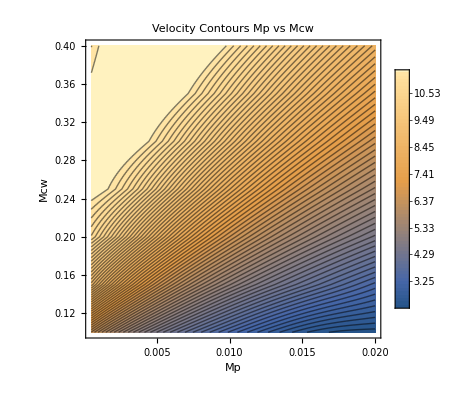

```mathematica
Countorv=ListContourPlot[Flatten[vDat,1],Contours->70, FrameLabel->{"Mp","Mcw" },Frame-> True, PlotLabel->"Velocity Contours Mp vs Mcw", PlotLegends->Automatic]
```